```mathematica
ClearAll["Global`*"];
```

```mathematica
(*initialization*)

(* for rational iteration *)
(* returns x^th number in the Calkin-Wilf sequence, see https://en.wikipedia.org/wiki/Calkin%E2%80%93Wilf_tree#Breadth_first_traversal *)
rationalCW[x_]:=Module[{b},
b=ToString[BaseForm[x,2]];
FromContinuedFraction[RunLengthEncode[Reverse[StringPart[b,1;;StringPosition[b," "][[1,1]]-2;;1]]]]
]
RunLengthEncode[x_List]:=If[First[x]=="1",Length[#]&/@Split[x],Join[{0},Length[#]&/@Split[x]]]

(* given rational (r,x), returns (m,y) that is a solution to S *)
ϕ[r_,x_]:={(-4-4 r-r^2-4 x^2-2 r x^2+x^4)/(8 r),(-4+r^2-4 x^2+x^4)/(2 r)};
(* given m and d, return gamma *)
gamma[m_,d_]:=Sqrt[2 d^4+8m d^2+16 m^2+16m](-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
(* double a point on the E.C. y^2 == x^3+ a x^2 + b x + c *)
doubleEC[{x_,y_},a_,b_,c_]:=Module[{newx,newy,λ,γ},
newx=(x^4-2b x^2-8c x+b^2-4a c)/(4(x^3+a x^2+b x+c));
λ=(3 x^2+2a x+b)/(2y);
γ=y-λ x;
newy=-(λ newx+γ);
Return[{newx,newy}];
]
(* add two points on the E.C. y^2 == x^3+ a x^2 + b x + c *)
addEC[{x1_,y1_},{x2_,y2_},a_,b_,c_]:=Module[{newx,newy,λ,ν},
If[x1==x2&&y1==y2,Return[doubleEC[{x1,y1},a,b,c]];];(*same point*)
If[x1==x2,Return[{0,ComplexInfinity}];];(*inverses*)
λ=(y2-y1)/(x2-x1);
ν=y1-λ x1;
newx=λ^2-a-x1-x2;
newy=-(λ newx+ν);
Return[{newx,newy}];
]
(* S -> C *)
tau[x_,y_,m_]:={y,4m+x^2+2,1};
(* C -> S *)
tauinv[Y_,M_,Z_,x_]:={x,Y/Z,(M-2Z-x^2 Z)/(4Z)};
(* A^2 -> C *)
sigma[r_,x_]:={x^4-4 x^2-4+r^2,x^4-4 x^2-4-r^2,2r};
(* C -> A^2 *)
sigmainv[Y_,M_,Z_]:=Module[{pos,neg},
pos=(8+Sqrt[64+8(8+Y+M)])/4;
neg=(8-Sqrt[64+8(8+Y+M)])/4;
If[pos≥0,
If[neg≥0,
(* randomly return one *)
Return[RandomSample[{{Z/2,Sqrt[pos]},{Z/2,Sqrt[neg]}},1][[1]]];
,
Return[{Z/2,Sqrt[pos]}];
]
,
Return[{Z/2,Sqrt[neg]}];
,
Return[{Z/2,Sqrt[pos]}];(* return positive by default, e.g. if symbolic *)
]];
```

```mathematica
{Y,M,Z}=sigma[69,420];
sigmainv[Y,M,Z]
```

{69,420}

```mathematica
sigmainv[a,b,c]
```

{c/2,1/2 √(8+√(64+8 (8+a+b)))}

We start with
	S: y^2==2 x^4+8m x^2+16 m^2+16m.
Then we apply the transformation
	τ: y↦Y/Z, 4m+x^2+2↦M/Z

This gives us the conic
	C: Y^2==M^2+(x^4-4 x^2-4)Z^2.
After this, we use the birational map
	σ : (r,x)↦(Y:M:Z)=(x^4+r^2-4 x^2-4:x^4-r^2-4 x^2-4:2r)
with inverse
	σ^-1: (Y:M:Z)↦(r,x)=(Z/2,√((4±√(32+2Y+2M))/2) ).
	
So we have a solution to the conic for every rational (r,x), by taking τ^-1(σ(r,x)). For easier notation, let ϕ=τ^-1∘σ. Then
	ϕ: (r,x) ↦(m,y)=((-4-4 r-r^2-4 x^2-2 r x^2+x^4)/(8 r),(-4+r^2-4 x^2+x^4)/(2 r)).
With inverse σ^-1∘τ:
	ϕ^-1: (m,y)↦(r,x)=()

```mathematica
(* Indeed, σ *)
Y=x^4+r^2-4 x^2-4;
M=x^4-r^2-4 x^2-4;
Z=2r;
{Y^2,M^2+(x^4-4 x^2-4)Z^2}//Expand//MatrixForm
```

(16-8 r^2+r^4+32 x^2-8 r^2 x^2+8 x^4+2 r^2 x^4-8 x^6+x^8
16-8 r^2+r^4+32 x^2-8 r^2 x^2+8 x^4+2 r^2 x^4-8 x^6+x^8)

```mathematica
(* finding τ^-1 *)
Solve[{
y==Y/Z,
x^2+4m+2==M/Z
},{m,y}]
```

{{m→(M-2 Z-x^2 Z)/(4 Z),y→Y/Z}}

```mathematica
(* finding ϕ = τ^-1∘σ *)
Y=x^4+r^2-4 x^2-4;
M=x^4-r^2-4 x^2-4;
Z=2r;
(*  (m,y) =   *){(M-2 Z-x^2 Z)/(4 Z),Y/Z}
```

{(-4-4 r-r^2-4 x^2-2 r x^2+x^4)/(8 r),(-4+r^2-4 x^2+x^4)/(2 r)}

```mathematica
f3NR={}; (* record parameter values that give f^3,f^2 newly reducible *)
f2NR={};
f1R={};
Do[Do[

m=ϕ[r,d][[1]];
γ=gamma[m,d];
f[x_]:=(x-γ)^2+γ+m;
If[IrreduciblePolynomialQ[f[x]],
If[IrreduciblePolynomialQ[f[f[x]]],
AppendTo[f3NR,{r,d}];
,
AppendTo[f2NR,{r,d}];
]
,
AppendTo[f1R,{r,d}];
]

,{r,0,100,1/16}],{d,1/2,1/2,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/8+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -3/1024+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::ivar: Indeterminate is not a valid variable.

IrreduciblePolynomialQ::poly: Indeterminate is not a polynomial.

```mathematica
f1R//MatrixForm
```

(21/8 | 1/2
17/4 | 1/2
49/8 | 1/2
33/4 | 1/2
85/8 | 1/2
53/4 | 1/2
129/8 | 1/2
77/4 | 1/2
181/8 | 1/2
105/4 | 1/2
241/8 | 1/2
137/4 | 1/2
309/8 | 1/2
173/4 | 1/2
385/8 | 1/2
213/4 | 1/2
469/8 | 1/2
257/4 | 1/2
561/8 | 1/2
305/4 | 1/2
661/8 | 1/2
357/4 | 1/2
769/8 | 1/2)

```mathematica
(* plotting gamma over (m,x) (m on horizontal axis) *)
T=Table[{},{i,-100,100}];
Do[Do[
m=ϕ[r,d][[1]];
γ=gamma[m,d];
AppendTo[T[[-d+101]],N[γ]];
,{r,-100,100}],{d,100,-100,-1}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 200000000+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -187500000000+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 192119202+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

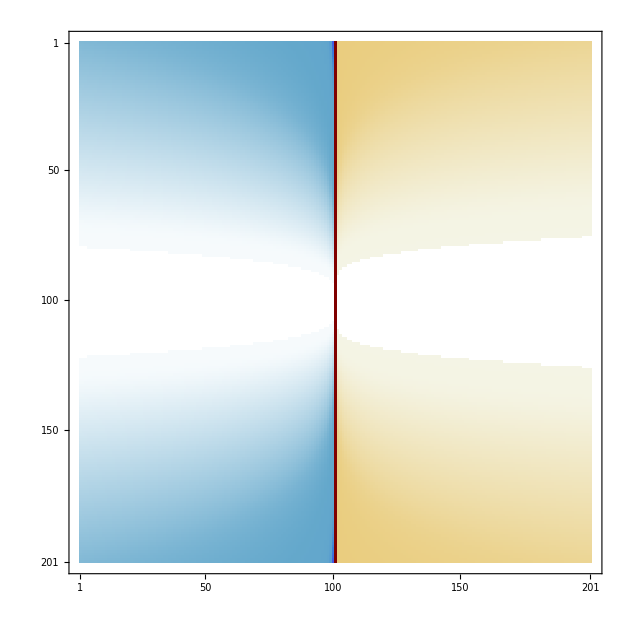

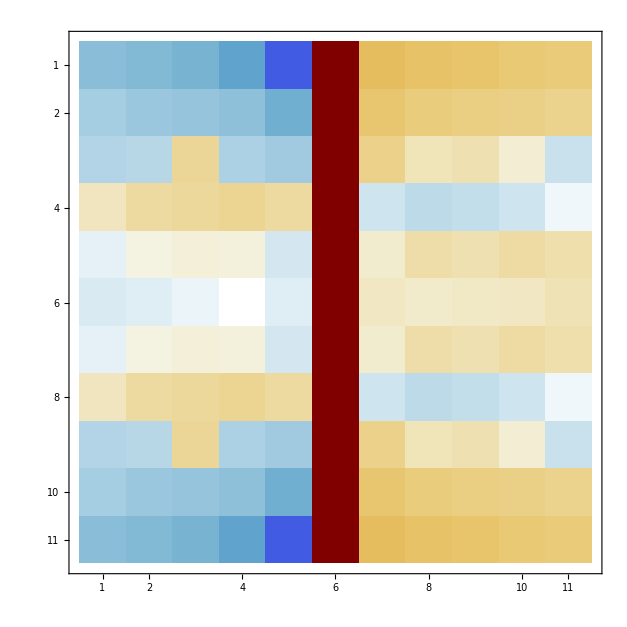

```mathematica
MatrixPlot[T]
MatrixPlot[Transpose[Transpose[T[[96;;106]]][[96;;106]]]]
```

```mathematica
(* if f is reducible then r=1/2(-4+d^2+q^2) or r=-(2 (-4-4 d^2+d^4))/(-4+d^2+q^2) for some q∈ℚ *)
```

```mathematica
m=ϕ[r,d][[1]];
γ=gamma[m,d]//Simplify
```

-1/(256 r^3)(-68 d^8 r^3-32 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+56 d^4 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+40 d^6 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)-8 d^2 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2-11 d^4 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2+d^2 (-d^4+2 d^2 (2+r)+(2+r)^2)^3+d^2 r √(((-4-4 d^2+d^4+r^2)^2)/r^2) (d^8+4 d^6 (-2+r)+(-4+r^2)^2+2 d^4 (4-8 r+5 r^2)-4 d^2 (-8+4 r+6 r^2+r^3)))

```mathematica
Collect[(x-γ)^2+γ+m,x]
```

```mathematica
(* when is √(a^2) = a? *)
Reduce[(-4-4 d^2+d^4+r^2)/r≥0,{d,r},Rationals]
```

(d|r)∈Rationals&&((d≤-√(2 (1+√2))&&r>0)||(-√(2 (1+√2))<d<√(2 (1+√2))&&(-√(4+4 d^2-d^4)≤r<0||r≥√(4+4 d^2-d^4)))||(d≥√(2 (1+√2))&&r>0))

```mathematica
Reduce[(-4-4 d^2+d^4+r^2)/r<0,{d,r},Rationals]
```

(d|r)∈Rationals&&((d≤-√(2 (1+√2))&&r<0)||(-√(2 (1+√2))<d<√(2 (1+√2))&&(r<-√(4+4 d^2-d^4)||0<r<√(4+4 d^2-d^4)))||(d≥√(2 (1+√2))&&r<0))

```mathematica
Plot3D[{(-4-4 d^2+d^4+r^2)/r,0},{d,-10,10},{r,-10,10},PlotRange->{-1000,1000}] (* case 1 orange is above blue, case 2 below*)
```

-Graphics3D-

```mathematica
(* Case 1. √(a^2) = a *)
γ=-1/(256 r^3)(-68 d^8 r^3-32 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+56 d^4 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+40 d^6 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)-8 d^2 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2-11 d^4 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2+d^2 (-d^4+2 d^2 (2+r)+(2+r)^2)^3+d^2 r (-4-4 d^2+d^4+r^2)/r (d^8+4 d^6 (-2+r)+(-4+r^2)^2+2 d^4 (4-8 r+5 r^2)-4 d^2 (-8+4 r+6 r^2+r^3)));
Simplify[-m-γ,r≠0]
```

-(d^2 (d^2-2 (2+r)) (-4+d^4+r^2-2 d^2 (2+r))^2)/(256 r^2)

```mathematica
(* If f is reducible, this must be a square, so -(d^2-2(2+r)) must be a square  *)
Solve[-d^2+2(2+r)== q^2,r]
```

{{r→1/2 (-4+d^2+q^2)}}

```mathematica
(* Case 2. √(a^2) = -a *)
γ=-1/(256 r^3)(-68 d^8 r^3-32 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+56 d^4 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+40 d^6 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)-8 d^2 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2-11 d^4 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2+d^2 (-d^4+2 d^2 (2+r)+(2+r)^2)^3+d^2 r (-4-4 d^2+d^4+r^2)/-r (d^8+4 d^6 (-2+r)+(-4+r^2)^2+2 d^4 (4-8 r+5 r^2)-4 d^2 (-8+4 r+6 r^2+r^3)));
Simplify[-m-γ,r≠0]
```

-(d^2 (-4+d^4+2 d^2 (-2+r)+r^2)^2 (2 d^4+d^2 (-8+r)-4 (2+r)))/(256 r^3)

```mathematica
(* Again this must be a square, so -(2 d^4+d^2(-8+r)-4(2+r))/r^3 must be a square. Multiplying by r^2 on both sides, *)
Solve[-(2 d^4+d^2(-8+r)-4(2+r))/r==q^2,r]
```

{{r→-(2 (-4-4 d^2+d^4))/(-4+d^2+q^2)}}

```mathematica
Plot3D[-(2 (-4-4 d^2+d^4))/(-4+d^2+q^2),{d,-10,10},{q,-10,10}]
```

-Graphics3D-

```mathematica
(* if f^2 is reducible... *)
```

```mathematica
m=ϕ[r,d][[1]];
γ=gamma[m,d]//Simplify
```

-1/(256 r^3)(-68 d^8 r^3-32 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+56 d^4 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+40 d^6 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)-8 d^2 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2-11 d^4 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2+d^2 (-d^4+2 d^2 (2+r)+(2+r)^2)^3+d^2 r √(((-4-4 d^2+d^4+r^2)^2)/r^2) (d^8+4 d^6 (-2+r)+(-4+r^2)^2+2 d^4 (4-8 r+5 r^2)-4 d^2 (-8+4 r+6 r^2+r^3)))

```mathematica
(* Case 1. √(a^2) = a *)
γ=-1/(256 r^3)(-68 d^8 r^3-32 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+56 d^4 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)+40 d^6 r^2 (-d^4+2 d^2 (2+r)+(2+r)^2)-8 d^2 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2-11 d^4 r (-d^4+2 d^2 (2+r)+(2+r)^2)^2+d^2 (-d^4+2 d^2 (2+r)+(2+r)^2)^3+d^2 r (-4-4 d^2+d^4+r^2)/r (d^8+4 d^6 (-2+r)+(-4+r^2)^2+2 d^4 (4-8 r+5 r^2)-4 d^2 (-8+4 r+6 r^2+r^3)));
Simplify[2(-m+√(m^2+m+γ)),r≠0]
```

(8-2 d^4+8 r+2 r^2+4 d^2 (2+r)+r √(((2-d^2+r)^2 (d^8-4 d^6 (2+r)+4 (2+r)^2+d^4 (8+12 r+5 r^2)+d^2 (32+32 r+4 r^2-2 r^3)))/r^2))/(8 r)

```mathematica
Reduce[d^8-4 d^6 (2+r)+4 (2+r)^2+d^4 (8+12 r+5 r^2)+d^2 (32+32 r+4 r^2-2 r^3)==q^2,{q,d,r}]
```

(d==0&&(r==1/2 (-4-q)||r==1/2 (-4+q)))||(d≠0&&(r==Root[-16-32 d^2-8 d^4+8 d^6-d^8+q^2+(-16-32 d^2-12 d^4+4 d^6) #1+(-4-4 d^2-5 d^4) #1^2+2 d^2 #1^3&,1]||r==Root[-16-32 d^2-8 d^4+8 d^6-d^8+q^2+(-16-32 d^2-12 d^4+4 d^6) #1+(-4-4 d^2-5 d^4) #1^2+2 d^2 #1^3&,2]||r==Root[-16-32 d^2-8 d^4+8 d^6-d^8+q^2+(-16-32 d^2-12 d^4+4 d^6) #1+(-4-4 d^2-5 d^4) #1^2+2 d^2 #1^3&,3]))

```mathematica
Solve[-16-32 d^2-8 d^4+8 d^6-d^8+q^2+(-16-32 d^2-12 d^4+4 d^6) x+(-4-4 d^2-5 d^4) x^2+2 d^2 x^3==0,x]
```

{{x→-(-4-4 d^2-5 d^4)/(6 d^2)-(-16-128 d^2-248 d^4-112 d^6-d^8)/(3 2^(2/3) d^2 (128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2+√(4 (-16-128 d^2-248 d^4-112 d^6-d^8)^3+(128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2)^2))^(1/3))+1/(6 2^(1/3) d^2)(128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2+√(4 (-16-128 d^2-248 d^4-112 d^6-d^8)^3+(128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2)^2))^(1/3)},{x→-(-4-4 d^2-5 d^4)/(6 d^2)+((1+ⅈ √3) (-16-128 d^2-248 d^4-112 d^6-d^8))/(6 2^(2/3) d^2 (128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2+√(4 (-16-128 d^2-248 d^4-112 d^6-d^8)^3+(128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2)^2))^(1/3))-1/(12 2^(1/3) d^2)(1-ⅈ √3) (128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2+√(4 (-16-128 d^2-248 d^4-112 d^6-d^8)^3+(128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2)^2))^(1/3)},{x→-(-4-4 d^2-5 d^4)/(6 d^2)+((1-ⅈ √3) (-16-128 d^2-248 d^4-112 d^6-d^8))/(6 2^(2/3) d^2 (128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2+√(4 (-16-128 d^2-248 d^4-112 d^6-d^8)^3+(128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2)^2))^(1/3))-1/(12 2^(1/3) d^2)(1+ⅈ √3) (128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2+√(4 (-16-128 d^2-248 d^4-112 d^6-d^8)^3+(128+1536 d^2+6048 d^4+9152 d^6+5400 d^8+528 d^10-2 d^12-108 d^4 q^2)^2))^(1/3)}}

```mathematica
(* the thing next to β could be 0 *)

Solve[(-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)==0,{m}]
```

{{m→1/4 (-2-2 d^2-√2 √(2+4 d^2-d^4))},{m→1/4 (-2-2 d^2+√2 √(2+4 d^2-d^4))}}

```mathematica
(* so d determines the value of m, as long as √2 √(2+4 d^2-d^4) is rational. *)
 Solve[2(2+4 d^2-d^4)==q^2,d]//FullSimplify
```

{{d→-√(2+√(6-q^2/2))},{d→√(2+√(6-q^2/2))},{d→-√(2-√(6-q^2/2))},{d→√(2-√(6-q^2/2))}}

```mathematica
Clear[m]
```

```mathematica
(* in this case, *)
(*m=1/4 (-2-2 d^2-√2 √(2+4 d^2-d^4));*)
γ=17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
-m-γ//Simplify
```

-1/64 d^2 (17 d^6+80 d^4 m+128 m^2 (1+m)+16 d^2 m (7+11 m))

```mathematica
m^2+m+γ//Factor
```

1/64 (17 d^8+112 d^4 m+80 d^6 m+64 m^2+128 d^2 m^2+176 d^4 m^2+128 d^2 m^3)

```mathematica
(*  *)
```